```mathematica
nn=10;
prec=32;
γ=1/2//N[#,prec]&;
λ=4/7//N[#,prec]&;
a0=λ//N[#,prec]&;
a1=(1-γ)/2//N[#,prec]&;
a2=(1+γ)/2//N[#,prec]&;
```

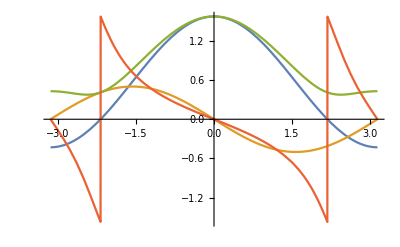

```mathematica
α[θ_]=(a0+(a2+a1) Cos[θ]);
β[θ_]=(a1-a2) Sin[θ];
ω[θ_]=Sqrt[α[θ]^2+β[θ]^2];
ϕ[θ_]=ArcTan[β[θ]/α[θ]];
Plot[{α[x],β[x],ω[x],ϕ[x]},{x,-π,π}]
```

```mathematica
mCos=Table[RandomInteger[{0,1}]-1/2,{j,nn}];
mSin=Table[RandomInteger[{0,1}]-1/2,{j,nn}];
mkPlus=(mCos+mSin)/2;
mkMinus=(mCos-mSin)/2;
```

```mathematica
MPlus=Table[mkPlus⟦k⟧ Exp[ⅈ ϕ[(2 π)/nn k]],{k,1,Length[mkPlus]}]//Fourier;
MMinus=Table[mkMinus⟦k⟧ Exp[ⅈ ϕ[(2 π)/nn k]],{k,1,Length[mkPlus]}]//Fourier;
```

```mathematica
cm=ToeplitzMatrix[Reverse[{c0,c1,c2,c3}],RotateRight[{c0,c1,c2,c3}]];
cm//MatrixForm
```

(c3 | c0 | c1 | c2
c2 | c3 | c0 | c1
c1 | c2 | c3 | c0
c0 | c1 | c2 | c3)